#### Dynamics of the rescaled variables (y_i=\chi_i \phi / (M \omega^-1))

```mathematica
ay1=y1*b*r1*(s*phi+phi-om)
ay2=y2*b*r2*(phi-om)
dy1=y1*b*r1*phi*c1*(phi+om)/2/M/omi
dy2=y2*b*r2*phi*c2*(phi+om)/2/M/omi
```

b r1 (-om+phi+phi s) y1

b (-om+phi) r2 y2

(b c1 phi (om+phi) r1 y1)/(2 M omi)

(b c2 phi (om+phi) r2 y2)/(2 M omi)

#### Dynamics of the conserved quantity

```mathematica
alp=y2*y1^(-r2/r1);
alpd1=Simplify[D[alp,y1]]
alpdd1=Simplify[D[alp,{y1,2}]]
alpd2=Simplify[D[alp,y2]]
alpdd2=Simplify[D[alp,{y2,2}]]
```

-(r2 y1^(-(r1+r2)/r1) y2)/r1

(r2 (r1+r2) y1^(-2-r2/r1) y2)/r1^2

y1^(-r2/r1)

0

```mathematica
aalp=Simplify[(alpd1*ay1+alpd2*ay2+alpdd1*dy1)/.{y1->z,y2->1-z,om->phi}]
dalp=Simplify[(alpd1^2*dy1+alpd2^2*dy2)/.{y1->z,y2->1-z,om->phi}]
```

-(b phi r2 (-1+z) z^(-(r1+r2)/r1) (c1 phi (r1+r2)-M omi r1 s z))/(M omi r1)

(b phi^2 r2 (-1+z) z^(-1-(2 r2)/r1) (c1 r2 (-1+z)-c2 r1 z))/(M omi r1)

#### Dynamics of the dynamics on the slow manifold

```mathematica
alpz=alp/.{y1->z,y2->1-z}
alpzd=Simplify[D[alpz,z]]
alpzdd=Simplify[D[alpz,{z,2}]]
```

(1-z) z^(-r2/r1)

(z^(-(r1+r2)/r1) (r2 (-1+z)-r1 z))/r1

(r2 z^(-2-r2/r1) (r1+r2+r1 z-r2 z))/r1^2

```mathematica
az=Simplify[aalp/alpzd-dalp*alpzdd/alpzd^3]
dz=Simplify[dalp/alpzd^2]
```

(b phi r1 r2 (-1+z) z (c1 phi r1 (r2 (-2+z)-r1 z)+M omi s (r2+r1 z-r2 z)^2+c2 phi r2 (r1+r2+r1 z-r2 z)))/(M omi (r2 (-1+z)-r1 z)^3)

-(b phi^2 r1 r2 (-1+z) z (c2 r1 z+c1 (r2-r2 z)))/(M omi (r2 (-1+z)-r1 z)^2)

```mathematica
az=FullSimplify[(az/.{M->Nt*phi*c2/omi,c1->c*c2,r1->r*r2,b->1})/.{phi->1,r2->1}]
dz=FullSimplify[(dz/.{M->Nt*phi*c2/omi,c1->c*c2,r1->r*r2,b->1})/.{phi->1,r2->1}]
```

(r (-1+z) z (1+r-z+r z+Nt s (1+(-1+r) z)^2+c r (-2+z-r z)))/(Nt (-1+z-r z)^3)

-(r (-1+z) z (c-c z+r z))/(Nt (1+(-1+r) z)^2)

```mathematica
betteraz=r*z*(1-z)/(r*z+1-z)*(s-(r*c-1+r*(c-1)/(r*z+1-z))/Nt/(r*z+1-z))
Reduce[betteraz==az]
```

(r (1-z) z (s-(-1+c r+((-1+c) r)/(1-z+r z))/(Nt (1-z+r z))))/(1-z+r z)

True

#### Invasion probability ratio from z

```mathematica
Intz=Integrate[az/dz,z]
Intz=Simplify[(Intz/.z->1)-(Intz/.z->0)]
```

(Nt (-1+r) s z)/(-c+r)-Log[1+(-1+r) z]+((-1+c) (c (1+r)-r (1+r+Nt s)) Log[c-c z+r z])/(c-r)^2

(-Nt (c-r) (-1+r) s-(-1+c) (c (1+r)-r (1+r+Nt s)) Log[c]+(r+c^2 r+Nt r s-c (1+r^2+Nt r s)) Log[r])/(c-r)^2

#### Dynamics for the frequency

```mathematica
Clear[x,z]
xx[z_]:=z/(z(1-c)+c)
zz[x_]:=c*x/(1-x(1-c))
dxx=FullSimplify[D[xx[z],z]/.{z->zz[x]}]
ddxx= FullSimplify[D[xx[z],{z,2}]/.{z->zz[x]}]
```

(1+(-1+c) x)^2/c

(2 (-1+c) (1+(-1+c) x)^3)/c^2

```mathematica
ax=FullSimplify[(dxx*az+dz*ddxx)/.{z->zz[x]}]
dx=FullSimplify[(dxx^2*dz)/.{z->zz[x]}]
```

-1/(Nt (1+(-1+c r) x)^3)r (-1+x) x (1+(-1+c) x) (-1+2 c+r-2 c r+Nt s-(-1+r) (4+c (-7+c (2+r))) x+2 Nt (-1+c r) s x+(-(-1+c) (-1+r) (5-4 c+(-2+c) c r)+Nt (-1+c r)^2 s) x^2+2 (-1+c)^2 (-1+r) (-1+c r) x^3)

-(r (-1+x) x (1+(-1+c) x)^3 (1+(-1+r) x))/(Nt (1+(-1+c r) x)^2)

```mathematica
betterax=(r (1-x) x(1-x+c x))/(1-x+r c x)(s-(1-x+c x)/(Nt (1-x+r c x))(r*c-1+(c-1)(r(1-x+c x)/(1-x+r c x)-2(r*x+1-x))))
Reduce[betterax==ax]
```

(r (1-x) x (1-x+c x) (s-((1-x+c x) (-1+c r+(-1+c) (-2 (1-x+r x)+(r (1-x+c x))/(1-x+c r x))))/(Nt (1-x+c r x))))/(1-x+c r x)

True

#### Invasion probability from the frequency

```mathematica
Int=Simplify[Integrate[(ax/dx),x]]
logPinv=Simplify[(Int/.x->1)-(Int/.x->0)-Log[c]]
```

(c Nt (-1+r) s)/((-1+c) (c-r) (1+(-1+c) x))-((c^2 (-2+r)+r (1-2 r+Nt s)-c (1+r^2+r (-4+Nt s))) Log[1+(-1+c) x])/(c-r)^2+((-1+c) (c (1+r)-r (1+r+Nt s)) Log[1+(-1+r) x])/(c-r)^2-Log[1-x+c r x]

((-c^2 (-1+r)+r (-1+r-Nt s)+c (1-2 r+r^2+Nt r s)) Log[c]+(-1+c) (c (1+r)-r (1+r+Nt s)) Log[r]-(c-r) (Nt (-1+r) s+(c-r) Log[c r]))/(c-r)^2

((1-c r) Log[c/r])/(c-r)+Nt s ((-1+r)/(-c+r)+((-1+c) r Log[c/r])/(-c+r)^2)

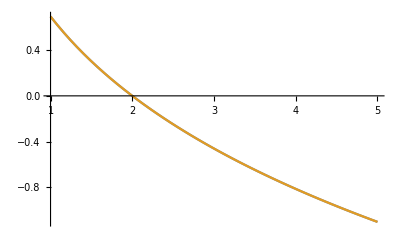

```mathematica
betterLogPinv=Nt s*((r-1)/(r-c)+r*(c-1)/(r-c)^2*Log[c/r]) + (1-r*c)/(c-r)*Log[c/r]
Plot[{betterLogPinv/.{s->2/Nt,c->2},logPinv/.{s->2/Nt,c->2}},{r,1,5}]
```

#### Integrals for the invasion probability

```mathematica
aux=(1+z(r c-1))/(1+z(r-1))/(1+z(c-1))^2
Simplify[Integrate[aux/.c->r,z]]
i11=Simplify[Integrate[aux,z]]/.z->1
i10=Simplify[Integrate[aux,z]]/.z->0
i1=FullSimplify[sM*(i11-i10)]
```

(1+(-1+c r) z)/((1+(-1+c) z)^2 (1+(-1+r) z))

-(2+r-2 z+2 r^2 z)/(2 (-1+r) (1+(-1+r) z)^2)

(((c-r) (-1+r))/(-1+c)+(-1+c) r Log[c]+(r-c r) Log[r])/(c-r)^2

(c (-1+r))/((-1+c) (c-r))

(sM (c-(1+c) r+r^2+(-1+c) r (Log[c]-Log[r])))/(c-r)^2

```mathematica
aux=(1/(1+z(r-1))/(1+z(c-1)))/.c->r
Integrate[aux,z]
i21=Simplify[Integrate[aux,z]]/.z->1
i20=Simplify[Integrate[aux,z]]/.z->0
i2=FullSimplify[(1-r c)*(i21-i20)]
```

1/(1+(-1+r) z)^2

-1/((-1+r) (1+(-1+r) z))

-1/((-1+r) r)

-1/(-1+r)

-c+1/r

```mathematica
aux=1/(1+z(r-1))/(1+z(r c-1))
Integrate[aux/.c->r,z]
i31=FullSimplify[Integrate[aux,z]]/.z->1
i30=FullSimplify[Integrate[aux,z]]/.z->0
i3=FullSimplify[-(c-1)*(i31-i30)]
```

1/((1+(-1+r) z) (1+(-1+c r) z))

(-Log[1+(-1+r) z]+Log[1+(-1+r^2) z])/((-1+r) r)

(Log[r]-Log[c r])/(r-c r)

0

(Log[r]-Log[c r])/r

```mathematica
aux=1/(1+z(c-1))
Integrate[aux,z]
i41=Simplify[Integrate[aux,z]]/.z->1
i40=Simplify[Integrate[aux,z]]/.z->0
i4=FullSimplify[2(c-1)*(i41-i40)]
```

1/(1+(-1+c) z)

Log[1+(-1+c) z]/(-1+c)

Log[c]/(-1+c)

0

2 Log[c]

```mathematica
FullSimplify[i1+i2+i3+i4]
```

2 Log[c]+(sM (c-(1+c) r+r^2+(-1+c) r (Log[c]-Log[r])))/(c-r)^2+((1-c r) (Log[c]-Log[r]))/(c-r)+(Log[r]-Log[c r])/r

```mathematica
aux=(1+z(r-1))/(r z+c(1-z))
i21=Simplify[Integrate[aux,z]]/.z->1
i20=Simplify[Integrate[aux,z]]/.z->0
i2=FullSimplify[(1-r c)*(i21-i20)]
```

(1+(-1+r) z)/(c (1-z)+r z)

((-1+r) (-c+r)+(r-c r) Log[r])/(c-r)^2

((r-c r) Log[c])/(c-r)^2

-((-1+c r) (c-(1+c) r+r^2+(-1+c) r (Log[c]-Log[r])))/(c-r)^2